# Data Science with Mathematica

## About the author

Author : Mok Lai Shun, Nelson.               
madeinquant@gmail.com

## Statistical Hypothesis Testing (t-test, chi-squared test & ANOVA)

### Performing the z-Score

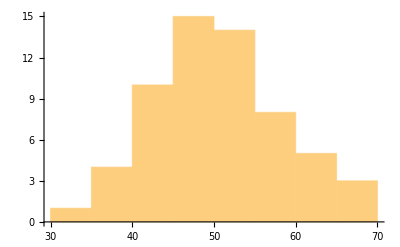

1.21641

```mathematica
Clear[classscore,zScore]
classscore=Round[RandomVariate[NormalDistribution[50,10],60]];
Histogram[classscore]
zScores = N[((classscore[[#]] - Mean[classscore])/ StandardDeviation[classscore])& /@ Range[Length[classscore]]];
zScore = N[((60 - Mean[classscore])/ StandardDeviation[classscore])]
```

```mathematica
(* probability of getting marks above 60 *)
1- CDF[NormalDistribution[0,1],zScore]
```

0.111915

```mathematica
(* how many students made it to the top 20% of the class? *)
InverseCDF[NormalDistribution[0,1],0.8] * StandardDeviation[classscore]+Mean[classscore]
(* how many students made it to the top 40% of the class? *)
InverseCDF[NormalDistribution[0,1],0.6] * StandardDeviation[classscore]+Mean[classscore]
```

56.8624

51.9376

### P-value

```mathematica
zScore = N[((68 - Mean[classscore])/ StandardDeviation[classscore])];
(* probability of getting marks above 68 *)
1- CDF[NormalDistribution[0,1],zScore]
(* 
So,you can see that the p-value is at 1.4% which is lower than the significance level.This means that the null hypothesis can be rejected and it can be said that it's not common to get 68 marks in mathematics. 
*)
```

0.0149273

### Performing the t-test

```mathematica
ClearAll[class1score,class2score]
class1score={45.0,40.0,49.0,52.0,54.0,64.0,36.0,41.0,42.0,34.0};class2score = {75.0,85.0,53.0,70.0,72.0,93.0,61.0,65.0,65.0,72.0};

TTest[{class1score,class2score}]
```

0.0000348207

### Performing the chi-squared test

```mathematica
(* The dice is rolled 36 times and the probability that each face should turn upwards is 1/6. *)
Clear[expected,observed]
expected={6,6,6,6,6,6.0};
observed={7,5,3,9,6,6.0};

Needs["HypothesisTesting`"]
data={observed,expected};
ChiSquarePValue[data,0.05]
```

OneSidedPValue→0.0000547992

### Performing the ANOVA

### Basic Data Analysis in Mathematica Please refer the details “http://numerics.io/basic-data-analysis/”

```mathematica
Clear[iris,properties,data,dataset]
iris = Import["https://archive.ics.uci.edu/ml/machine-learning-databases/iris/iris.data"];
iris = Delete[iris, Length[iris]] ;
properties = {"SepalLength","SepalWidth","PetalLength","PetalWidth","Species"};
data = Association[MapIndexed[(First[properties[[#2]]]-> #1) &, Transpose@iris]];
dataset = Dataset[data]
```

SepalLength | 5.1 | 4.9 | 4.7 | 4.6 | 5. | 5.4 | 4.6 | 5. | 4.4 | 4.9 | 5.4 | 4.8 | 4.8 | 4.3 | 5.8 | 5.7 | ⋯_134
SepalWidth | 3.5 | 3. | 3.2 | 3.1 | 3.6 | 3.9 | 3.4 | 3.4 | 2.9 | 3.1 | 3.7 | 3.4 | 3. | 3. | 4. | 4.4 | 
PetalLength | 1.4 | 1.4 | 1.3 | 1.5 | 1.4 | 1.7 | 1.4 | 1.5 | 1.4 | 1.5 | 1.5 | 1.6 | 1.4 | 1.1 | 1.2 | 1.5 | 
PetalWidth | 0.2 | 0.2 | 0.2 | 0.2 | 0.2 | 0.4 | 0.3 | 0.2 | 0.2 | 0.1 | 0.2 | 0.2 | 0.1 | 0.1 | 0.2 | 0.4 | 
Species | Iris-setosa | Iris-setosa | Iris-setosa | Iris-setosa | Iris-setosa | Iris-setosa | Iris-setosa | Iris-setosa | Iris-setosa | Iris-setosa | Iris-setosa | Iris-setosa | Iris-setosa | Iris-setosa | Iris-setosa | Iris-setosa | 
2 levels | 5rows |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | Dataset[<|"SepalLength" -> _, "SepalWidth" -> _, "PetalLength" -> _, "PetalWidth" -> _, "Species" -> _|>]